```mathematica
Abs[Re[Re[Cos[t]]+I*Re[Sin[t]]]]
```

Abs[Re[Cos[t]]]

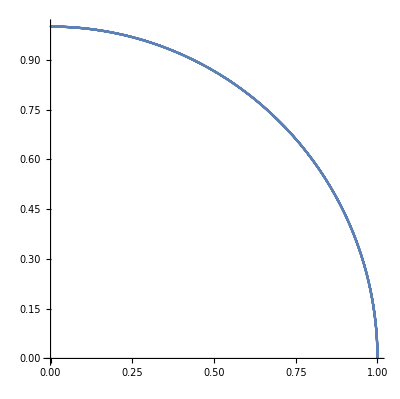

```mathematica
c0=ParametricPlot[Abs[{Re[Cos[t]],Re[Sin[t]]}],{t,0,2 Pi}]
```

```mathematica
ϕ[z_]:=1/2z +1/2
```

```mathematica
ϕ[Re[Cos[t]]+I Re[Sin[t]]]
```

1/2+1/2 (Re[Cos[t]]+ⅈ Re[Sin[t]])

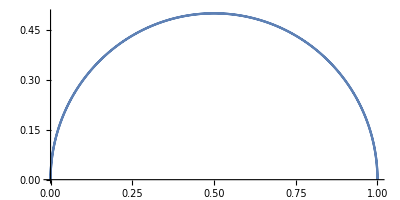

```mathematica
c1=ParametricPlot[{Abs[Re[ϕ[Re[Cos[t]]+I Re[Sin[t]]]]],Abs[Im[ϕ[Re[Cos[t]]+I Re[Sin[t]]]]]},{t,0,2 Pi}]
```

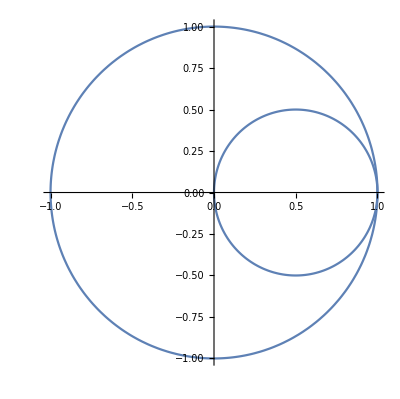

```mathematica
Show[c0,c1]
```